# WL—Training for Programmers 3

## String Patterns

String patterns work a lot like expression patterns

String patterns can be given names and used with RuleDelayed in StringReplace and StringCases

See the String Patterns guide page for details

Many expression patterns can be used in string patterns

Sequences: __ and ___

Alternatives: "Carlo"|"Bob"|"Vitaliy"

Named: x_ and x:(…)

Qualifiers: Longest, Shortest, Except

StringExpression is the container that holds the elements of the string pattern

The infix notation is __~~__

There are several symbolic patterns

Semantic classes: Whitespace, NumberString, DatePattern

Character classes: WordCharacter, LetterCharacter, DigitCharacter, WhitespaceCharacter, PunctuationCharacter, HexadecimalCharacter

Anchors: WordBoundary, StartOfString, EndOfString

### Examples

```mathematica
(exampleData=Import["meetings.txt","Lines"])//Column
```

12:00am Bhubanjyoti Bhattacharya & Bernat
12:15am Andrey Grabovsky & Bernat
3:15pm Connor Bain & Carlo
3:30pm Jackreece Ejini & Carlo
3:45pm Daavid Vaananen & Ian
4:00pm Les Grundman & Ian
4:15pm Daniel Reynolds & Matthew
4:30pm Monica Linden & Matthew
4:45pm Leo McElroy & Matthew
5:00pm Christopher DeFiglia & Matthew
5:15pm Hikari Sorenson & Giulio
5:30pm Nae Eoun Lee & Giulio
8:30pm Sung Min Yoon & Matthew
8:45pm Ethan Truelove & Timothee
9:00pm Carlos Manual Rodriguez Martinez & Timothee
9:15pm Rohan Saxena & Matteo
9:30pm Benjamin Keller & Timothee
9:45pm Soham Pal & Timothee
10:00pm Rian Shams & Timothee
10:15pm Emilio Andres Vazquz & Bob

Let’s get the lines for Matt’s students

```mathematica
StringCases[exampleData,___~~"Matthew"~~___]
```

{{},{},{},{},{},{},{4:15pm Daniel Reynolds & Matthew},{4:30pm Monica Linden & Matthew},{4:45pm Leo McElroy & Matthew},{5:00pm Christopher DeFiglia & Matthew},{},{},{8:30pm Sung Min Yoon & Matthew},{},{},{},{},{},{},{}}

```mathematica
Cases[exampleData,line_/;StringMatchQ[line,___~~"Matthew"~~___]]//Column
```

4:15pm Daniel Reynolds & Matthew
4:30pm Monica Linden & Matthew
4:45pm Leo McElroy & Matthew
5:00pm Christopher DeFiglia & Matthew
8:30pm Sung Min Yoon & Matthew

Who are Matt’s students?

```mathematica
Join@@StringCases[exampleData,Except[WhitespaceCharacter]..~~" "~~student__~~" & Matthew"~~___:>student]
```

{Daniel Reynolds,Monica Linden,Leo McElroy,Christopher DeFiglia,Sung Min Yoon}

When does Matt have to be present?

```mathematica
Join@@StringCases[exampleData,StartOfString~~time__~~" "~~___~~"Matthew"~~___:>TimeObject[time]]
```

{16:15:00GMT-4.TimeObject[{16,15,0.},TimeZone→-4.],16:30:00GMT-4.TimeObject[{16,30,0.},TimeZone→-4.],16:45:00GMT-4.TimeObject[{16,45,0.},TimeZone→-4.],17:00:00GMT-4.TimeObject[{17,0,0.},TimeZone→-4.],20:30:00GMT-4.TimeObject[{20,30,0.},TimeZone→-4.]}

Let’s “translate” the lines into German

```mathematica
StringReplace[exampleData,StartOfString~~time__~~meridian:("am"|"pm")~~" "~~student__~~" & "~~instructor__~~EndOfString:>DateString[time<>meridian,{"Hour24",":","Minute"}]<>" "<>student<>" und "<>instructor]//Column
```

00:00 Bhubanjyoti Bhattacharya und Bernat
00:15 Andrey Grabovsky und Bernat
15:15 Connor Bain und Carlo
15:30 Jackreece Ejini und Carlo
15:45 Daavid Vaananen und Ian
16:00 Les Grundman und Ian
16:15 Daniel Reynolds und Matthew
16:30 Monica Linden und Matthew
16:45 Leo McElroy und Matthew
17:00 Christopher DeFiglia und Matthew
17:15 Hikari Sorenson und Giulio
17:30 Nae Eoun Lee und Giulio
20:30 Sung Min Yoon und Matthew
20:45 Ethan Truelove und Timothee
21:00 Carlos Manual Rodriguez Martinez und Timothee
21:15 Rohan Saxena und Matteo
21:30 Benjamin Keller und Timothee
21:45 Pal und Timothee
22:00 Rian Shams und Timothee
22:15 Emilio Andres Vazquz und Bob

## More on Data Processing

### Padding ragged lists

```mathematica
raggedLists={{"t","h","e"},{"q","u","i","c","k"},{"b","r","o","w","n"},{"f","o","x"},{"j","u","m","p","e","d"},{"o","v","e","r"},{"t","h","e"},{"l","a","z","y"},{"d","o","g"}};
```

```mathematica
Grid[raggedLists]
```

t | h | e |  |  | 
q | u | i | c | k | 
b | r | o | w | n | 
f | o | x |  |  | 
j | u | m | p | e | d
o | v | e | r |  | 
t | h | e |  |  | 
l | a | z | y |  | 
d | o | g |  |  |

```mathematica
?PadRight
```

PadRight[list,n] makes a list of length n by padding list with zeros on the right. 
PadRight[list,n,x] pads by repeating the element x. 
PadRight[list,n,{x_1,x_2,…}] pads by cyclically repeating the elements x_i. 
PadRight[list,n,padding,m] leaves a margin of m elements of padding on the left. 
PadRight[list,{n_1,n_2,…}] makes a nested list with length n_i at level i. 
PadRight[list] pads a ragged array list with zeros to make it full.

```mathematica
PadRight[raggedLists,Automatic,"⎵"]//Grid
```

t | h | e | ⎵ | ⎵ | ⎵
q | u | i | c | k | ⎵
b | r | o | w | n | ⎵
f | o | x | ⎵ | ⎵ | ⎵
j | u | m | p | e | d
o | v | e | r | ⎵ | ⎵
t | h | e | ⎵ | ⎵ | ⎵
l | a | z | y | ⎵ | ⎵
d | o | g | ⎵ | ⎵ | ⎵

```mathematica
PadLeft[raggedLists,Automatic,""]//Grid
```

|  |  | t | h | e
 | q | u | i | c | k
 | b | r | o | w | n
 |  |  | f | o | x
j | u | m | p | e | d
 |  | o | v | e | r
 |  |  | t | h | e
 |  | l | a | z | y
 |  |  | d | o | g

### Side effects

```mathematica
𝒟ℬ=Dataset[{<|"name"->"Bill","age"->32,"gender"->♂|>,<|"name"->"Alice","gender"->♀,"age"->28|>}]
```

Dataset[<>]

```mathematica
insert[record_]:=AppendTo[𝒟ℬ,record]
```

```mathematica
transactions={<|"name"->"Wan","gender"->♀|>,<|"name"->"Berta","age"->17,"gender"->♀|>,<|"name"->"Paulo","age"->27,"gender"->♂|>};
```

```mathematica
Scan[insert,transactions]
```

```mathematica
𝒟ℬ
```

Dataset[<>]

### Some useful functional paradigms

#### Thread

```mathematica
Thread[{4,{3,2,1}}]
```

{{4,3},{4,2},{4,1}}

```mathematica
Thread[{𝒳,𝒴,𝒵}->𝒜]
```

{𝒳→𝒜,𝒴→𝒜,𝒵→𝒜}

```mathematica
Thread[{α,β,γ}->{0.4102,0.4375,0.4801}]
```

{α→0.4102,β→0.4375,γ→0.4801}

```mathematica
AssociationThread[{α,β,γ}->{0.4102,0.4375,0.4801}]
```

<|α→0.4102,β→0.4375,γ→0.4801|>

#### Through

```mathematica
size=({{9, 0, 10, 2, 5, 0, 7}, {5, 3, 5, 10, 4, 0, 3}, {1, 9, 7, 6, 4, 4, 8}, {1, 6, 2, 8, 7, 10, 8}, {6, 7, 4, 7, 9, 7, 10}, {2, 10, 8, 0, 0, 4, 2}, {0, 8, 9, 5, 1, 8, 3}});
```

```mathematica
Through[{Min,Max}[size]]
```

{0,10}

#### MapThread

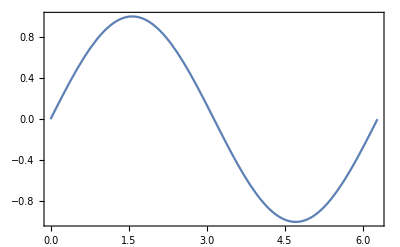
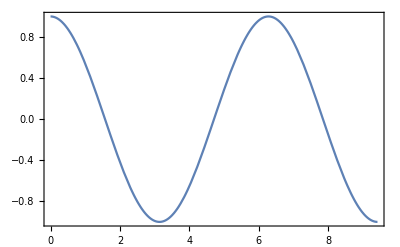
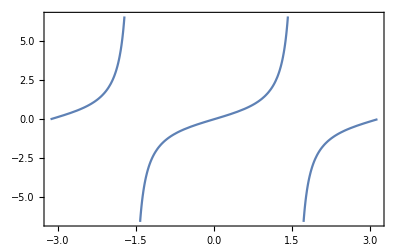

```mathematica
MapThread[Plot,{{Sin[x],Cos[y],Tan[z]},{{x,0,2π},{y,0,3π},{z,-π,π}}}]
```

Question from audience: can you show the three plots overlaid?

ColorData[97] is the color function used for the default plot theme.

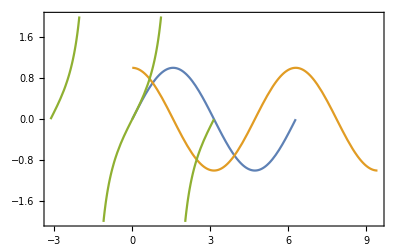

```mathematica
Show@@MapThread[Plot[#1,#2,PlotRange->{All,{-2,2}},PlotStyle->#3]&,{{Sin[x],Cos[y],Tan[z]},{{x,0,2π},{y,0,3π},{z,-π,π}},ColorData[97]/@{1,2,3}}]//Legended[#,LineLegend[ColorData[97]/@{1,2,3},{Sin[x],Cos[y],Tan[z]}]]&
```

#### ReplaceAllRepeated

```mathematica
tree={1,{{2,{{4,{}},{5,{}},{6,{}}}},{3,{{7,{}},{8,{{9,{}}}}}}}};
```

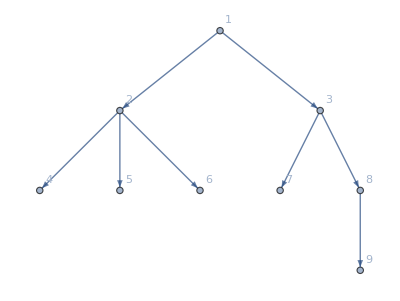

```mathematica
showTree[tree]
```

```mathematica
rule={root_Integer,branches:{___}}:>𝒯[root,branches];
```

```mathematica
tree/.rule
```

𝒯[1,{{2,{{4,{}},{5,{}},{6,{}}}},{3,{{7,{}},{8,{{9,{}}}}}}}]

```mathematica
tree=tree//.rule
```

𝒯[1,{𝒯[2,{𝒯[4,{}],𝒯[5,{}],𝒯[6,{}]}],𝒯[3,{𝒯[7,{}],𝒯[8,{𝒯[9,{}]}]}]}]

## Stacks, Queues, and Linked Lists

Stacks, queues, and linked lists are useful data structures

often used as components of algorithms

Wolfram Language does not have built-in forms of these structures

The package StackQueue.m implements these structures along with constructors, deconstructors, and methods

A stack uses nested Lists

A queue uses two stacks

A linked list uses DownValues (original idea from Danny Lichtblau)

```mathematica
<<StackQueue`
```

StackQueue.m, $Revision: 1.7 $).
	Direct queries to Robert Nachbar, rnachbar@wolfram.com.

```mathematica
?StackQueue
```

StackQueue.m is a package that provides efficient stack and queue functions.

### Stacks

Elements are pushed onto the top of a stack

Elements are popped off the top of a stack

```mathematica
stackInfo[]
```

EmptyStackQ[stack] returns True if stack is empty and False otherwise.

```mathematica
InitializeStack[𝒮]
```

```mathematica
Push[𝒮,"abc"]
```

```mathematica
Push[𝒮,123]
```

```mathematica
Push[𝒮,{5,6,7}]
```

```mathematica
PrintStack[𝒮]
```

{5,6,7}

123

abc

```mathematica
FetchStack[𝒮]
```

{abc,123,{5,6,7}}

```mathematica
Pop[𝒮]
```

{5,6,7}

```mathematica
Pop[𝒮]
```

123

```mathematica
Pop[𝒮]
```

abc

```mathematica
Pop[𝒮]
```

Pop::empty: 𝒮 has length 0 and no top element.

Pop[𝒮]

```mathematica
ClearStack[𝒮]
```

```mathematica
Pop[𝒮]
```

Pop::stack: 𝒮 is not a stack.

Pop[𝒮]

### Queues

Elements are enqueued at the back of a queue

Elements are dequeued from the front of a queue

Elements are requeued at the front of the queue (in this implementation)

```mathematica
queueInfo[]
```

```mathematica
InitializeQueue[𝒬]
```

```mathematica
Enqueue[𝒬,π]
```

```mathematica
Enqueue[𝒬,17]
```

```mathematica
Enqueue[𝒬,{"x","y","z"}]
```

```mathematica
PrintQueue[𝒬]
```

π

17

{x,y,z}

```mathematica
Dequeue[𝒬]
```

π

```mathematica
Dequeue[𝒬]
```

17

```mathematica
Dequeue[𝒬]
```

{x,y,z}

```mathematica
Dequeue[𝒬]
```

Dequeue::empty: 𝒬 has length 0 and no front element.

Dequeue[𝒬]

```mathematica
ClearQueue[𝒬]
```

```mathematica
Dequeue[𝒬]
```

Dequeue::queue: 𝒬 is not a queue.

Dequeue[𝒬]

### (Linked)Lists

Elements are inserted at the end of a linked list

Elements are never deleted from a linked list (in this implementation)

Elements of a linked list can be retrieved by position (counting from the beginning)

```mathematica
linkedListInfo[]
```

PartList[list, i] returns the ith element of list.

```mathematica
InitializeList[ℒ]
```

```mathematica
LengthList[ℒ]
```

0

```mathematica
InsertList[ℒ,π]
```

```mathematica
InsertList[ℒ,N@π]
```

```mathematica
LengthList[ℒ]
```

2

```mathematica
PartList[ℒ,1]
```

π

```mathematica
PartList[ℒ,4]
```

PartList::partw: Part 4 of ℒ does not exist.

```mathematica
PrintList[ℒ]
```

π

3.14159

```mathematica
InsertList[ℒ,{a,b}]
InsertList[ℒ,17]
```

```mathematica
FetchList[ℒ]
```

{π,3.14159,{{{t,h,e},{q,u,i,c,k},{b,r,o,w,n},{f,o,x},{j,u,m,p,e,d},{o,v,e,r},{t,h,e},{l,a,z,y},{d,o,g}},b},17}

```mathematica
ClearList[ℒ]
```

```mathematica
LengthList[ℒ]
```

LengthList::list: ℒ is not a list.

LengthList[ℒ]

## Debugging

Most developers rely on instrumented code to find bugs

Unlike compiled languages, adding Print or Echo will generally not cause to code to evaluate differently

### Echo

Echo prints its input and then returns it

{3,7,10,1,10,6,9,9,8,4}

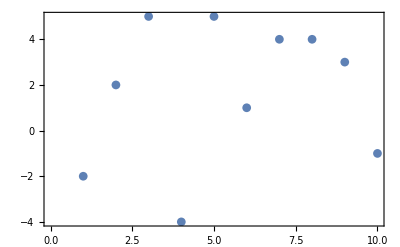

```mathematica
RandomInteger[{0,10},10]//Echo//Map[#-5&,#]&//ListPlot
```

Instrument code to follow data processing

```mathematica
munge[dataIn_]:=Module[{data=dataIn},
data=1/data;
data=3data+6;
data=1/data;
data^2
]
```

```mathematica
testData={-3/4,3/2,3/4,3/5,-1/2,-1,-3,1/2,-3/5,-1};
```

```mathematica
munge[testData]
```

Power::infy: Infinite expression 1/0 encountered.

{1/4,1/64,1/100,1/121,ComplexInfinity,1/9,1/25,1/144,1,1/9}

```mathematica
munge[dataIn_]:=Module[{data=dataIn},
data=1/data//Echo[#,"after division"]&;
data=3data+6//Echo[#,"after addition"]&;
data=1/data//Echo[#,"after second division"]&;
data^2
]
```

```mathematica
munge[testData]
```

after division {-4/3,2/3,4/3,5/3,-2,-1,-1/3,2,-5/3,-1}

after addition {2,8,10,11,0,3,5,12,1,3}

Power::infy: Infinite expression 1/0 encountered.

after second division {1/2,1/8,1/10,1/11,ComplexInfinity,1/3,1/5,1/12,1,1/3}

{1/4,1/64,1/100,1/121,ComplexInfinity,1/9,1/25,1/144,1,1/9}

### TracePrint

```mathematica
tree
```

𝒯[1,{𝒯[2,{𝒯[4,{}],𝒯[5,{}],𝒯[6,{}]}],𝒯[3,{𝒯[7,{}],𝒯[8,{𝒯[9,{}]}]}]}]

```mathematica
dfsPre[𝒯[root_,branches:{___}]]:=Prepend[Join@@dfsPre/@branches,root]
dfsPost[𝒯[root_,branches:{___}]]:=Append[Join@@dfsPost/@branches,root]
```

```mathematica
TracePrint[dfsPre[tree],_dfsPre]
```

dfsPre[tree]

dfsPre[𝒯[1,{𝒯[2,{𝒯[4,{}],𝒯[5,{}],𝒯[6,{}]}],𝒯[3,{𝒯[7,{}],𝒯[8,{𝒯[9,{}]}]}]}]]

dfsPre[𝒯[2,{𝒯[4,{}],𝒯[5,{}],𝒯[6,{}]}]]

dfsPre[𝒯[4,{}]]

dfsPre[𝒯[5,{}]]

dfsPre[𝒯[6,{}]]

dfsPre[𝒯[3,{𝒯[7,{}],𝒯[8,{𝒯[9,{}]}]}]]

dfsPre[𝒯[7,{}]]

dfsPre[𝒯[8,{𝒯[9,{}]}]]

dfsPre[𝒯[9,{}]]

{1,2,4,5,6,3,7,8,9}

```mathematica
TracePrint[dfsPre[tree],dfsPre[𝒯[3,_]]]
```

dfsPre[𝒯[3,{𝒯[7,{}],𝒯[8,{𝒯[9,{}]}]}]]

{1,2,4,5,6,3,7,8,9}

```mathematica
bfs[tree_𝒯]:=bfs[{tree}]
bfs[queue:{f_,r___}]:=Prepend[bfs[Join[{r},Last@f]],First@f]
bfs[{}]:={}
```

```mathematica
bfs[tree]
```

{1,2,3,4,5,6,7,8,9}

## Initialization

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
e[𝒯[r_,b_]]:=Join[r->First[#]&/@b,Join@@e/@b]
showTree[tree_]:=Graph[e[tree],VertexLabels->"Name"]
```

```mathematica
stackInfo[]:=DeleteCases[Names["StackQueue`*Stack*"|"StackQueue`Push"|"StackQueue`Pop"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```

```mathematica
queueInfo[]:=DeleteCases[Names["StackQueue`*ueue*"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```

```mathematica
linkedListInfo[]:=DeleteCases[Names["StackQueue`*List*"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```